```mathematica
"Ahmad Bosset Ali
ID:804-635-447
Email:bossetali@gmail.com
HW#2"

ClearAll["Global`*"]
```

```mathematica
" I could not finish 2 and 4 "
```

Problem #1

{{x[t]→1/2 (a t^2+2 t v0+2 x0)}}

1/2 (a t^2+2 t v0+2 x0)

1/2 (10+9.32 t+0.67 t^2)

1/2 (9.32+1.34 t)

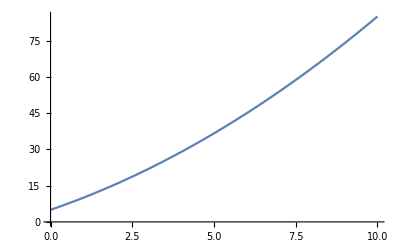

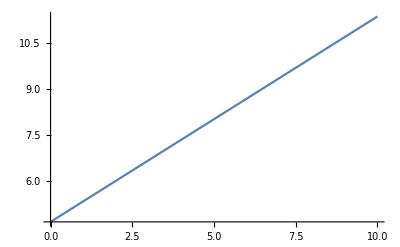

```mathematica
"Problem #1"
DSolve[{x''[t]==a,x'[0]==v0,x[0]==x0},x[t],t]
x[t_]=  1/2 (a t^2+2 x0+2 t v0)
position[t_]=x[t]/.x0->5/.v0-> 4.66/.a-> .67

velocity[t_]=x'[t]/.x0->0/.v0-> 4.66/.a-> .67

Plot[position[t],{t,0,10 }]

Plot[velocity[t],{t,0,10}]


ClearAll["Global`*"]
```

```mathematica
ClearAll["Global`*"]

"Problem #2"
```

```mathematica
ClearAll["Global`*"]
eqn1:= m x1''[t_]=+k x2[t]-2k x1[t]

eqn2:=m x2''[t_]=+k x1[t]-2k x2[t]

x1'[0]=0;
x2'[0]=0;
x1[0]=0;
x2[0]=l;

eqnlist1={eqn1,eqn2,x1[t],x2[t],x1'[t],x2'[t]}

eqnlist2={eqn1,eqn2}

qlist={x1,x2}

soln=DSolve[eqnlist2,qlist,t];

soln[[1]]
ClearAll["Global`*"]
```

Set::write: Tag Times in (m (-2 k x1[t_]+k x2[t_]))/m is Protected.

Set::write: Tag Times in (m (k x1[t_]-2 k x2[t_]))/m is Protected.

{-2 k x1[t]+k x2[t],k x1[t]-2 k x2[t],x1[t],x2[t],x1'[t],x2'[t]}

Set::write: Tag Times in (m (-2 k x1[t_]+k x2[t_]))/m is Protected.

Set::write: Tag Times in (m (k x1[t_]-2 k x2[t_]))/m is Protected.

{-2 k x1[t]+k x2[t],k x1[t]-2 k x2[t]}

{x1,x2}

DSolve::deqn: Equation or list of equations expected instead of -2 k x1[t]+k x2[t] in the first argument {-2 k x1[t]+k x2[t],k x1[t]-2 k x2[t]}.

{-2 k x1[t]+k x2[t],k x1[t]-2 k x2[t]}

```mathematica
ClearAll["Global`*"]
```

```mathematica
"Problem #3"

DSolve[{x''[t]+2b x'[t]+w0^2  x[t]==0},x[t],t]
```

Problem #3

{{x[t]→ⅇ^(t (-b-√(b^2-w0^2))) C[1]+ⅇ^(t (-b+√(b^2-w0^2))) C[2]}}

{a ⅇ^(t (-b-√(b^2-w0^2)))+ⅇ^(t (-b+√(b^2-w0^2)))}

5 ⅇ^((-π/7-1/7 ⅈ √195 π) t)+ⅇ^((-π/7+1/7 ⅈ √195 π) t)

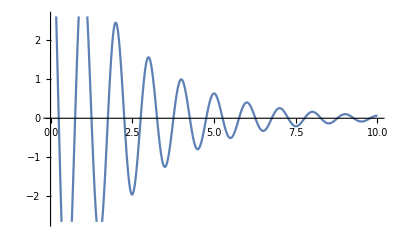

{a ⅇ^(t (-b-√(b^2-w0^2)))+ⅇ^(t (-b+√(b^2-w0^2)))}

5 ⅇ^((-(5 π)/7-3/7 ⅈ √19 π) t)+ⅇ^((-(5 π)/7+3/7 ⅈ √19 π) t)

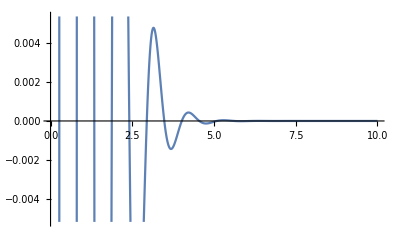

{a ⅇ^(t (-b-√(b^2-w0^2)))+ⅇ^(t (-b+√(b^2-w0^2)))}

6 ⅇ^(-2 π t)

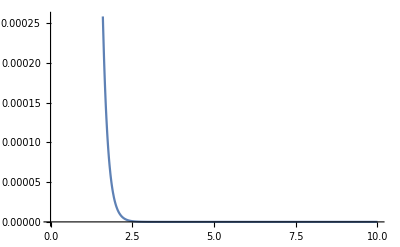

{5 ⅇ^((-b-√(b^2-4 π^2)) t)+ⅇ^((-b+√(b^2-4 π^2)) t)}

oddly it wouldnt let me use b but w works, and it gives the proper program still, also if not working try running again

```mathematica
{x[t_]=ⅇ^(t (-b-√(b^2-w0^2))) a+ⅇ^(t (-b+√(b^2-w0^2))) }

position[t_]=x[t]/.a->5/.w0-> 2 Pi /.b-> Pi/7


Plot[Re[position[t]],{t,0,10 }]

ClearAll["Global`*"]

{x[t_]=ⅇ^(t (-b-√(b^2-w0^2))) a+ⅇ^(t (-b+√(b^2-w0^2))) }

position[t_]=x[t]/.a->5/.w0-> 2 Pi /.b-> 5 Pi/7


Plot[Re[position[t]],{t,0,10 }]

ClearAll["Global`*"]

{x[t_]=ⅇ^(t (-b-√(b^2-w0^2))) a+ⅇ^(t (-b+√(b^2-w0^2))) }

position[t_]=x[t]/.a->5/.w0-> 2 Pi /.b-> 2Pi


Plot[Re[position[t]],{t,0,10 }]

ClearAll["Global`*"]
{x[t_]=ⅇ^(t (-b-√(b^2-w0^2))) a+ⅇ^(t (-b+√(b^2-w0^2))) /.a->5/.w0-> 2 Pi/.b->b}

"oddly it wouldnt let me use b but w works, and it gives the proper program still, also if not working try running again"

Manipulate[Plot[Re[x[t]/.b-> w],{t,0,10 }],{w,0,4 Pi}]
```

```mathematica
"Problem #4" 

ClearAll["Global`*"]

a=f/m

v=Integrate[a,t]

x=Integrate[v,t]
```

Problem #4

f/m

(f t)/m

(f t^2)/(2 m)